# Recurrence Relationships

An m term linear constant coefficient recurrence
	a_n=c_1 a_(n-1)+c_2 a_(n-2)+…+c_m a_(n-m)
 defines the sequence a_1,a_2,… from initial condition a_1,a_(2,)…,a_m and the coefficients c_1,c_2,…,c_m.   A recurrence is stable if all initial conditions generate sequences that decay to zero.

The BDF formula on the Dahlquist test problem y'=λ y are of this form.  We want to understand when all the solutions of the BDF recurrence decay to zero.  We are looking for a computable condition on the coefficients that ensures all the solutions decay to zero.

## Messing Around

Lets try to find some parameter values where recurrence relations do not blow up!

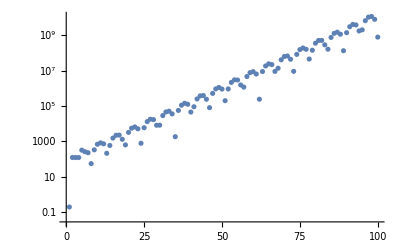

```mathematica
{c1,c2,c3}={1.2,0.2,-1.2};
{a1,a2,a3}={-0.2,124.2,-123.4};
Clear[a]
{a[1],a[2],a[3]}={a1,a2,a3};
a[n_]:=a[n]=c1*a[n-1]+c2*a[n-2]+c3*a[n-3]
ListLogPlot[Table[Abs[a[i]],{i, 1,100}]]
```

## Theory

A linear constant coefficient recurrence relation
(1)	a_n=c_1 a_(n-1)+c_2 a_(n-2)+…+c_m a_(n-m)
generically has a general solution of the form
	a_n=α_1 λ_1^n+α_2 λ_2^n+…+α_m λ_m^n
where the λs are the roots of the “polynomial” found by plugging in a_n=λ^n 
	λ^n=c_1 λ^(n-1)+c_2 λ^(n-2)+…+c_m λ^(n-m)
It really is a polynomial! If you divide by λ^n 
	1=c_1 λ^-1+c_2 λ^-2+…+c_m λ^-m
and then multiply by λ^m you get
(2)	λ^m=c_1 λ^(m-1)+c_2 λ^(m-2)+…+c_m λ^(m-m)
which always has m roots and almost always has m distinct roots.

If you put this together then some solutions of the recurrence (1) blow up if any of the roots of the characteristic polynomial have absolute value bigger than 1 and all solutions decay if all the roots have absolute value less than 1.

We are now in the position to compute stability regions for our multi-step BDF formulas.

## BDF-2

Our formula (which we have derived from interpolation) are conveniently listed at  https://en.wikipedia.org/wiki/Backward_differentiation_formula.
Remember we assess stability on the linear test problem y'=λ y and interpret things in terms of the scaled step z=λ h for each eigenvalue of Df for real world ODE systems y'=f(y).

BDF 2 is 
	y_(n+2)-4/3 y_(n+1)+1/3 y_n=2/3 h f(t_(n+2),y_(n+2))
On our test problem this gives
	y_(n+2)-4/3 y_(n+1)+1/3 y_n=2/3 h λ y_(n+2)=2/3 z y_(n+2)
The characteristic polynomial for this comes from simplifying
	λ^(n+2)-4/3 λ^(n+1)+1/3 λ^n=2/3 z λ^(n+2)
which is simply
	λ^2-4/3 λ^1+1/3 λ^0=2/3 z λ^2
or equivalently
	(1-2/3 z)λ^2-4/3 λ+1/3=0.
The quadratic formula gives
	λ=(-2+±√(1+2z))/(2z - 3)
We can plot the border curves we want directly.  We need to interpret where one of the curves has gone and which side of the curves is good.

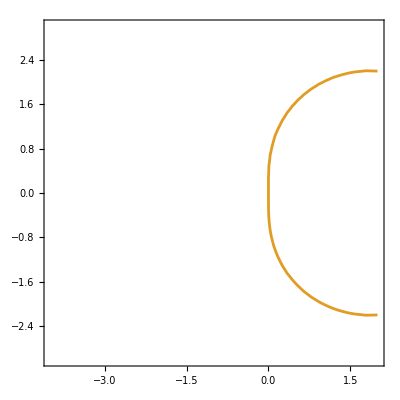

```mathematica
f1[z_]:=(-2+√(1+2 z))/(-3+2 z)
f2[z_]:=(-2-√(1+2 z))/(-3+2 z)
ContourPlot[
{Abs[f1[x+ I y]]==1,
Abs[f2[x+ I y]]==1
},
{x, -4,2},
{y,-3,3},Axes->True]
```

It is not clear that we can do the higher order BDFs the same way!  This will always work but it might be slow.

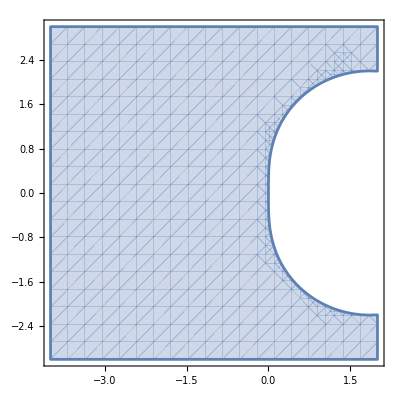

```mathematica
f[z_]:=Max[Abs[NSolveValues[(1-2/3 z)λ^2-4/3 λ+1/3==0,λ]]]
RegionPlot[ f[x+I y]<1,{x, -4,2},
{y,-3,3},Axes->True,MaxRecursion->2]
```

```mathematica
(1-2/3 z)λ^2-4/3 λ+1/3=0
```

## BDF-3

Remember we assess stability on the linear test problem y'=λ y and interpret things in terms of the scaled step z=λ h for each eigenvalue of Df for real world ODE systems y'=f(y).

BDF 3 is 
	y_(n+3)-18/11 y_(n+2)+9/11 y_(n+1)-2/11 y_n=6/11 h f(t_(n+3),y_(n+3))
On our test problem this gives the char poly
	λ^3-18/11 λ^2+9/11 λ-2/11=6/11 z  λ^3
The cubic formula is probably not helpful!

It is not clear that we can do the higher order BDFs the same way!  This will always work but it might be slow.

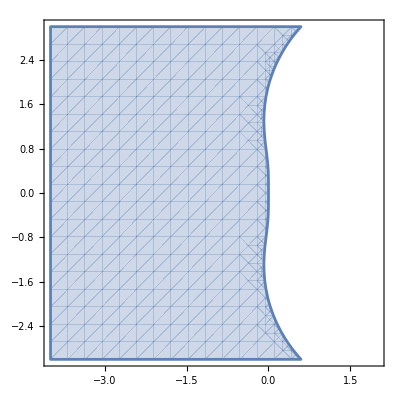

```mathematica
f[z_]:=Max[Abs[NSolveValues[(1-6/11 z)λ^3-18/11 λ^2+9/11 λ-2/11==0,λ]]]
RegionPlot[ f[x+I y]<1,{x, -4,2},
{y,-3,3},Axes->True,MaxRecursion->2]
```

```mathematica
2
```